```mathematica
$FeynCalcStartupMessages=False;
Needs["FeynCalc`"];

mZnum=91.1876;mHnum=125.25;vevnum=246.0;
GFnum=1.1663787*10^-5;sw2num=0.23126;
cw2num=1-sw2num;cwnum=Sqrt[cw2num];
mWnum=mZnum*cwnum;
gnum=Sqrt[8*mWnum^2*GFnum/Sqrt[2]];
gVnum=-1/2+2*sw2num;gAnum=-1/2;
GeVtoPb=0.3893793656*10^9;

FCClearScalarProducts[];
Ebeam=Sqrt[s]/2;pmag=Sqrt[s]/2;
EZ=(s+mZ^2-mH^2)/(2*Sqrt[s]);
EH=(s+mH^2-mZ^2)/(2*Sqrt[s]);
kallen=s^2+mZ^4+mH^4-2*s*mZ^2-2*s*mH^2-2*mZ^2*mH^2;
kmag=Sqrt[kallen]/(2*Sqrt[s]);
SP[p1,p1]=0;SP[p2,p2]=0;
SP[k1,k1]=mZ^2;SP[k2,k2]=mH^2;
SP[p1,p2]=s/2;
SP[p1,k1]=Ebeam*EZ-pmag*kmag*cth;
SP[p2,k1]=Ebeam*EZ+pmag*kmag*cth;
SP[p1,k2]=Ebeam*EH+pmag*kmag*cth;
SP[p2,k2]=Ebeam*EH-pmag*kmag*cth;

vertexEEZ[mu_]:=-I*g/(2*cw)*GA[mu].(gV-gA*GA[5]);
vertexHZZ[nu_,rho_]:=I*(2*mZ^2/vev)*MT[nu,rho];
propagatorZ[mu_,nu_]:=-I*MT[mu,nu]/(s-mZ^2);

amplitudeRaw=SpinorVBar[p2,0].vertexEEZ[mu].SpinorU[p1,0]*propagatorZ[mu,nu]*vertexHZZ[nu,rho]*Pair[Momentum[Polarization[k1,I]],LorentzIndex[rho]];

amplitude=Contract[amplitudeRaw]//DiracSimplify//FCFactorOut[#,-I*g*mZ^2/(vev*cw*(s-mZ^2))]&;
amplitude//TraditionalForm

amplitudeCC=ComplexConjugate[amplitude];
msqRaw=amplitude*amplitudeCC;
msqSpins=(1/4)*FermionSpinSum[msqRaw];
msqPols=DoPolarizationSums[msqSpins,k1]//Contract;
msqAveraged=msqPols//DiracSimplify//ExpandScalarProduct//Simplify;
msqAveraged//TraditionalForm

dSigmadOmega=1/(64*Pi^2*s)*(kmag/pmag)*msqAveraged//ExpandScalarProduct//Simplify;
dSigmadOmega//TraditionalForm

sigmaTotal=2*Pi*Integrate[dSigmadOmega,{cth,-1,1}]//Simplify;
sigmaTotal//TraditionalForm

numericalRules={g->gnum,cw->cwnum,gV->gVnum,gA->gAnum,vev->vevnum,mZ->mZnum,mH->mHnum};
sigmaPb[sqrtS_?NumericQ]:=(sigmaTotal/. numericalRules/. s->sqrtS^2)*GeVtoPb;
resultTable=Table[{sVal,sigmaPb[sVal]},{sVal,{250,350,500}}];
TableForm[resultTable,TableHeadings->{None,{"Sqrt[s] (GeV)","sigma (pb)"}}]
```

-(ⅈ g mZ^2 (gV (φ(-OverBar[p2])).(γ̄·ε̄(k1)).(φ(OverBar[p1]))-gA (φ(-OverBar[p2])).(γ̄·ε̄(k1)).(γ̄)^5.(φ(OverBar[p1]))))/(cw vev (s-mZ^2))

-(g^2 mZ^2 (gA^2+gV^2) ((cth^2-1) mH^4-2 (cth^2-1) mH^2 (mZ^2+s)+(cth^2-1) mZ^4-2 (cth^2+3) mZ^2 s+(cth^2-1) s^2))/(8 cw^2 vev^2 (mZ^2-s)^2)

-(g^2 mZ^2 (gA^2+gV^2) √(mH^4-2 mH^2 (mZ^2+s)+(mZ^2-s)^2) ((cth^2-1) mH^4-2 (cth^2-1) mH^2 (mZ^2+s)+(cth^2-1) mZ^4-2 (cth^2+3) mZ^2 s+(cth^2-1) s^2))/(512 π^2 cw^2 s^2 vev^2 (mZ^2-s)^2)

(g^2 mZ^2 (gA^2+gV^2) √(mH^4-2 mH^2 (mZ^2+s)+(mZ^2-s)^2) (mH^4-2 mH^2 (mZ^2+s)+mZ^4+10 mZ^2 s+s^2))/(192 π cw^2 s^2 vev^2 (mZ^2-s)^2)

Sqrt[s] (GeV) | sigma (pb)
250 | 0.237899
350 | 0.128231
500 | 0.0568874

```mathematica
(*Cross section in pb as a function of sqrt(s),reusing the analytic sigmaTotal*)sigmaPbPlot[sqrtS_?NumericQ]:=(sigmaTotal/. numericalRules/. s->sqrtS^2)*GeVtoPb;

(*Threshold energy*)
thresholdE=mZnum+mHnum;

(*Main figure:sigma(sqrt(s)) from 220 to 1000 GeV*)
figSigma=Plot[sigmaPbPlot[rs],{rs,220,1000},PlotRange->{0,All},Frame->True,FrameLabel->{"\!\(\*SqrtBox[\(s\)]\) (GeV)","σ(\!\(\*SuperscriptBox[\(e\), \(+\)]\)\!\(\*SuperscriptBox[\(e\), \(-\)]\)→ZH) (pb)"},GridLines->{{thresholdE},None},GridLinesStyle->Directive[Red,Dashed],Epilog->{Text[Style["threshold \!\(\*SubscriptBox[\(m\), \(Z\)]\)+\!\(\*SubscriptBox[\(m\), \(H\)]\)",12],{thresholdE+60,0.02}]},PlotStyle->Thick,ImageSize->500];
figSigma

(*Locate the peak numerically*)
peak=NMaximize[{sigmaPbPlot[rs],230<rs<300},rs]

(*Log-log plot to exhibit the~1/s falloff at high energy*)
figLogLog=LogLogPlot[{sigmaPbPlot[rs],sigmaPbPlot[500]*(500/rs)^2},{rs,300,3000},Frame->True,FrameLabel->{"\!\(\*SqrtBox[\(s\)]\) (GeV)","σ (pb)"},PlotLegends->{"exact","∝1/s reference"},PlotStyle->{Thick,Dashed},ImageSize->500];
figLogLog

(*Angular distribution (normalized) at three energies*)
figAngular=Plot[Evaluate[Table[(dSigmadOmega/. numericalRules/. s->rs^2)/(sigmaTotal/. numericalRules/. s->rs^2)*2*Pi,{rs,{250,350,500}}]],{cth,-1,1},Frame->True,FrameLabel->{"cosθ","(1/σ) dσ/dcosθ"},PlotLegends->{"250 GeV","350 GeV","500 GeV"},ImageSize->500];
figAngular
```

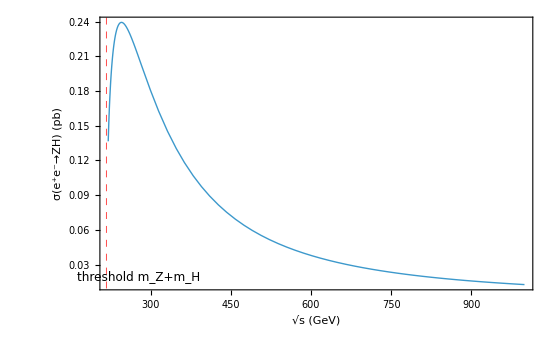
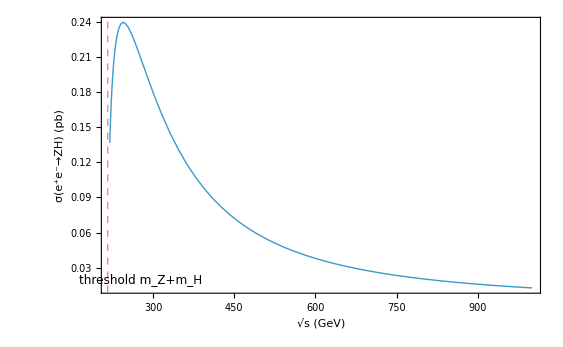

{0.239299,{rs→244.836}}